```mathematica
PlotSurf[surffname_]:=Module[{surfs,surfshapes},
surfs=Import[surffname, "Table",HeaderLines->9, "FieldSeperators"->" ", "LineSeperators"->"\n"];
surfshapes=Flatten@Table[Line[{{s[[2]],s[[3]]},{s[[4]],s[[5]]}}],{s,surfs}];
Graphics[Join[{Directive[{Thin,Red}]},surfshapes],ImageSize->Large]
]
```

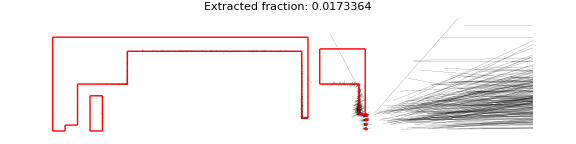

```mathematica
(*dir="/home/cal/Documents/DSMC_Simulations/4_8_20_Yuiki_cell/2sccm/data/";*)
dir="/home/cal/Documents/DSMC_Simulations/4_3_20_flow_gap_length/flow_4.000_gap_0.003_len_0.010/data/";
data=Import[StringJoin[dir,"particles.out"],"Table",HeaderLines->1]/.{{}->Nothing,"Inf"->0,"-Inf"->0};
flow=Import[StringJoin[dir,"DS2FF.500000.DAT"],"Table",HeaderLines->9];
surfs=PlotSurf[StringJoin[dir,"cell.510000.surfs"]];
flow=Select[flow,#[[3]]>0&];
z=data[[;;,4]];
y=data[[;;,3]];
x=data[[;;,2]];
outside=Position[z,x_/;x>0.09];
r=√(x^2+y^2);
znext=data[[;;,7]];
ynext=data[[;;,6]];
xnext=data[[;;,5]];
rnext=√(xnext^2+ynext^2);
vx=data[[;;,8]];
vy=data[[;;,9]];
vz=data[[;;,10]];
v=√(vx^2+vy^2+vz^2);
collides=data[[;;,-2]];
times=data[[;;,-1]];
lines=Table[Line[{{z[[i]],r[[i]]},{znext[[i]],rnext[[i]]}}],{i,Length@data}];
extraction=N[Length@outside/Length@z];
trajs=Show[Graphics[{Thickness[0.00005],lines},PlotRange->{{0,0.12},{0,0.03}},PlotLabel->StringForm["Extracted fraction: ``",extraction]],surfs,ImageSize->Large]
```

```mathematica
stats=Row[{Histogram[vz[[Flatten[outside]]],Automatic,"Probability",PlotLabel->"Forward Velocity (m/s)",ImageSize->Small],
Histogram[times[[Flatten[outside]]]1000,Automatic,"Probability",
PlotLabel->"Extraction Time (ms)",ImageSize->Small],
Histogram[collides[[Flatten[outside]]]/1000,Automatic,"Probability",
PlotLabel->"Collisions (x10^3)",ImageSize->Small]}];
```

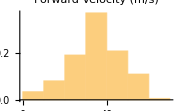
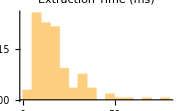
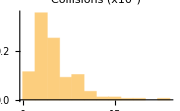
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
Column[{trajs,stats}]
```

```mathematica
Column[{Show[ListDensityPlot[flow[[;;,{1,2,6}]],ImageSize->Large,InterpolationOrder->0,PlotLegends->Automatic,AspectRatio->0.03/0.12,PlotLabel->"Z Velocity (m/s)",ColorFunction->"TemperatureMap",PlotRange->All],(*trajs,*)surfs],
Show[ListDensityPlot[flow[[;;,{1,2,7}]],ImageSize->Large,InterpolationOrder->0,PlotLegends->Automatic,AspectRatio->0.03/0.12,PlotLabel->"Radial Velocity (m/s)",ColorFunction->"TemperatureMap",PlotRange->All],(*trajs,*)surfs],
Show[ListDensityPlot[Transpose@{flow[[;;,1]],flow[[;;,2]],Log10[flow[[;;,4]]]-6},ImageSize->Large,InterpolationOrder->0,PlotLegends->Automatic,AspectRatio->0.03/0.12,PlotLabel->"Log_10 Density (1/cm^3)",PlotRange->All,
ColorFunction->"TemperatureMap"],(*trajs,*)surfs],
Show[ListDensityPlot[flow[[;;,{1,2,3}]],ImageSize->Large,InterpolationOrder->0,PlotLegends->Automatic,AspectRatio->0.03/0.12,PlotLabel->"Temperature (K)",PlotRange->All,
ColorFunction->"TemperatureMap"],(*trajs,*)surfs]
}]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-